# Straightening at a Scale

Can straightness over a local horizon produce a globally shortest extension? We fix an incoming path, extend it by ten steps, and increase the horizon used to test each continuation. The resulting beam can change from walks that curl back toward the starting region to shortest paths that leave it.

```mathematica
Needs[ "WolframInstitute`InfraGeometry`" ]
```

## A beam at a scale

A walk is geodesic at infra-scale r if each subwalk of at most r edges is a shortest path between its ends. At r==∞, the whole walk must be shortest. A germ is the initial shortest path; here it has eight edges and ends at the graph centre. The beam consists of its ten-step extensions that satisfy the scale-r condition.

SelectInfraWalk with "From" -> "MostVisited" chooses the members with the largest total occupation count along their vertices and edges. Counts include repeated visits, so this selection can favour a walk that returns to a busy region. We keep all ties.

The rows below are the trihexagonal, truncated square and rhombitrihexagonal tilings. The columns use r==3,4,6, so each row shows the change as the horizon grows. The beam is orange and the selected members are red; the incoming germ is drawn last. All shortest-path and occupation calculations use graph distances.

```mathematica
GraphicsGrid[ Table[
  With[
    { g = Graph[ TessellationNeighborhoodGraph[ configuration, 14 ], Sequence @@ InfraSubstrateStyle[ "Large" ] ] },
    { centre = First @ GraphCenter[ g ] },
    { start = First @ Keys @ InfraMeasurement[ g, InfraShell[ centre, 8 ], "VertexDensity" ] },
    { germ = First @ RandomInfraSegment[ g, InfraSegment[ start, centre ], 1, RandomSeeding -> 1 ] },
    { walks = RandomInfraGeodesic[ g, germ, r, { 10 }, All ] },
    Labeled[
      InfraSubstrateHighlight[ g, {
        walks -> StandardOrange,
        SelectInfraWalk[ g, walks, All, "From" -> "MostVisited" ] -> StandardRed,
        InfraWalk[ germ ] -> StandardOrange }, "ThicknessRange" -> { 1.25, 3.75 } ],
      Row[ { configuration, ", r = ", r } ] ] ],
  { configuration, { { 3, 6, 3, 6 }, { 4, 8, 8 }, { 3, 4, 6, 4 } } },
  { r, { 3, 4, 6 } } ], ImageSize -> 1000 ]
```

-Graphics-

A small horizon permits a return around a face whose shorter subwalks are still shortest. Increasing r removes such returns from the beam. The sets of admissible walks shrink, but their most visited members need not vary monotonically: the occupation counts change with the beam.

## A local rule can miss a complete turn

On the cycle graph C_q with q≥3, follow the edges repeatedly in one direction. A subwalk of k≤q edges has endpoint distance min(k,q-k). It is shortest precisely when k≤⌊q/2⌋. Thus arbitrarily many complete turns satisfy every horizon r≤⌊q/2⌋, although each complete turn returns to its starting vertex. A horizon of ⌊q/2⌋+1 detects a shortcut as soon as that many edges have been traversed.

The two panels use the same twelve-cycle in its native layout. At horizon six, the orange half-cycle and its blue complement have equal length. At horizon seven, the seven orange edges have a five-edge blue shortcut. This exact obstruction depends on the length of a cycle, not its apparent roundness in the drawing.

```mathematica
GraphicsRow[
  Table[
    With[
      { g = CycleGraph[ 12, Sequence @@ InfraSubstrateStyle[ "Medium" ] ] },
      { forward = Range[ r + 1 ], complement = Join[ { 1 }, Range[ 12, r + 1, -1 ] ] },
      Labeled[
        InfraSubstrateHighlight[ g, {
          InfraWalk[ forward ] -> StandardOrange,
          InfraWalk[ complement ] -> StandardBlue, { 1, r + 1 } -> StandardRed },
          "ThicknessRange" -> { 2, 5 } ],
        Row[ { "r = ", r, ": ", r, " edges versus ", 12 - r } ] ] ],
    { r, { 6, 7 } } ],
  ImageSize -> 900 ]
```

-Graphics-

Consequently, local straightness alone cannot guarantee global straightness on arbitrary graphs. The lattice experiments test whether the occupation-based selection suppresses these returns before the horizon itself excludes them.

## The same rule on meshes

The rows below are large square, cube and sphere meshes; the columns use horizons r==2,4,6. Each panel starts from a six-edge germ and samples 128 continuations of at most eight further steps. Each step chooses an admissible neighbour uniformly. The sample is orange, its most visited members red, and the incoming germ blue. Selection here is relative to this finite sample. The points and walks are chosen entirely from graph distances; the layouts are illustrations.

```mathematica
GraphicsGrid[
  Table[
    With[
      { g = BlockRandom[ InfraSubstrate[ specification[[ 1 ]], "Large" ], RandomSeeding -> 2 ] },
      { centre = First @ GraphCenter[ g ] },
      { start = First @ Keys @ InfraMeasurement[ g, InfraShell[ centre, 6 ], "VertexDensity" ] },
      { germ = First @ RandomInfraSegment[ g, InfraSegment[ start, centre ], 1, RandomSeeding -> 1 ] },
      { walks = RandomInfraGeodesic[ g, germ, r, UpTo[ 8 ], UpTo[ 128 ],
          "NextVertexFunction" -> RandomChoice, RandomSeeding -> 1 ] },
      Labeled[
        InfraSubstrateHighlight[ g, {
          walks -> StandardOrange,
          SelectInfraWalk[ g, walks, All, "From" -> "MostVisited" ] -> StandardRed,
          InfraWalk[ germ ] -> StandardBlue }, "ThicknessRange" -> { 1.25, 3.75 } ],
        Row[ { specification[[ 2 ]], ", r = ", r } ] ] ],
    { specification, {
        { "SquareMeshGraph", "square mesh" }, { "CubeMeshGraph", "cube mesh" },
        { "SphereMeshGraph", "sphere mesh" } } },
    { r, { 2, 4, 6 } } ],
  ImageSize -> 1200 ]
```

-Graphics-

## Measuring straightness

Let η==(x_0,…,x_m) be the extension after removing the incoming germ, while retaining their common vertex x_0. Its normalized excess is

E(η)==(m-d(x_0,x_m))/m.

This is zero exactly when the extension is a shortest path. For the unit-edge planar embedding φ, also measure

A(η)==1/m max_i dist(φ(x_i),[φ(x_0),φ(x_m)]).

This second quantity measures deviation from a Euclidean chord. A graph shortest path may still be a staircase with positive chord deviation. Returning to the three lattices, the next pictures isolate the selected extensions at r==6. The incoming germ is blue, the extensions red and their Euclidean chords dashed orange. The staircase shape remains visible even when the graph excess is zero.

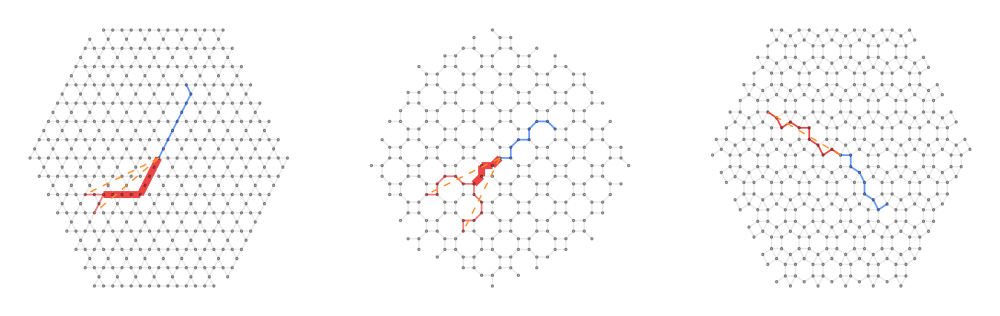

```mathematica
GraphicsRow[
  Table[
    With[
      { g = Graph[ TessellationNeighborhoodGraph[ configuration, 14 ], Sequence @@ InfraSubstrateStyle[ "Large" ] ] },
      { centre = First @ GraphCenter[ g ],
        coordinates = AssociationThread[ VertexList[ g ], GraphEmbedding[ g ] ] },
      { start = First @ Keys @ InfraMeasurement[ g, InfraShell[ centre, 8 ], "VertexDensity" ] },
      { germ = First @ RandomInfraSegment[ g, InfraSegment[ start, centre ], 1, RandomSeeding -> 1 ] },
      { walks = RandomInfraGeodesic[ g, germ, 6, { 10 }, All ] },
      { selected = SelectInfraWalk[ g, walks, All, "From" -> "MostVisited" ] },
      { extensions = Map[
          walk |-> Drop[ Last /@ SortBy[ VertexList[ walk ], First ], Length[ germ ] - 1 ], selected ] },
      InfraSubstrateHighlight[ g, { selected -> StandardRed, InfraWalk[ germ ] -> StandardBlue },
        Epilog -> { StandardOrange, Dashed,
          Map[ path |-> Line[ Lookup[ coordinates, { First[ path ], Last[ path ] } ] ], extensions ] } ,
        "ThicknessRange" -> { 1.25, 5 } ] ],
    { configuration, { { 3, 6, 3, 6 }, { 4, 8, 8 }, { 3, 4, 6, 4 } } } ],
  ImageSize -> 1000 ]
```

Each plotted value below is the maximum over all tied most visited members.

```mathematica
With[
  { readouts = Table[
      With[
        { g = TessellationNeighborhoodGraph[ configuration, 14 ] },
        { centre = First @ GraphCenter[ g ], distances = GraphDistanceMatrix[ g ],
          coordinates = AssociationThread[ VertexList[ g ], GraphEmbedding[ g ] ] },
        { start = First @ Keys @ InfraMeasurement[ g, InfraShell[ centre, 8 ], "VertexDensity" ] },
        { germ = First @ RandomInfraSegment[ g, InfraSegment[ start, centre ], 1, RandomSeeding -> 1 ] },
        Table[
          With[
            { walks = RandomInfraGeodesic[ g, germ, r, { 10 }, All ] },
            { extensions = Map[
                walk |-> Drop[ Last /@ SortBy[ VertexList[ walk ], First ], Length[ germ ] - 1 ],
                SelectInfraWalk[ g, walks, All, "From" -> "MostVisited" ] ] },
            { { r, Max @ Map[
                  path |-> 1 - distances[[ VertexIndex[ g, First[ path ] ], VertexIndex[ g, Last[ path ] ] ]] /
                    ( Length[ path ] - 1 ), extensions ] },
              { r, Max @ Map[
                  path |-> Max[ RegionDistance[
                    Line[ Lookup[ coordinates, { First[ path ], Last[ path ] } ] ], Lookup[ coordinates, path ] ] ] /
                    ( Length[ path ] - 1 ), extensions ] } } ],
          { r, 2, 10 } ] ],
      { configuration, { { 3, 6, 3, 6 }, { 4, 8, 8 }, { 3, 4, 6, 4 } } } ] },
  GraphicsRow[ {
    ListLinePlot[ readouts[[ All, All, 1 ]], PlotRange -> All, AxesLabel -> { "r", "E" },
      PlotLegends -> { "trihexagonal", "truncated square", "rhombitrihexagonal" } ],
    ListLinePlot[ readouts[[ All, All, 2 ]], PlotRange -> All, AxesLabel -> { "r", "A" },
      PlotLegends -> { "trihexagonal", "truncated square", "rhombitrihexagonal" } ] }, ImageSize -> 1000 ] ]
```

-Graphics-

In this finite sweep, the excess first vanishes at r==4 on the trihexagonal tiling, r==6 on the truncated square tiling and r==5 on the rhombitrihexagonal tiling, and remains zero through r==10. A zero excess means every selected extension is shortest; it says nothing by itself about continuing the germ's Euclidean direction. Once r≥m==10, every admissible extension must be shortest because the horizon contains that whole extension. Straightening at a smaller r therefore measures the effect of selecting the most visited members before the local constraint forces it.

## Comparing resolutions

This experiment changes the observation horizon on a fixed substrate and a fixed extension length. A comparison across resolutions would instead grow the germ length, extension length m and horizon r together, keeping their ratios fixed. Lengths in the pictures would be divided by m, while E and A already have no units. Scale consistency would mean that these normalized readouts approach stable functions of r/m. The present finite sweep does not establish that limit.

Two questions remain. At fixed r, do the selected extensions approach rays as their allowed length grows, and how does this depend on the germ? On meshes without the same preferred lattice directions, does the selected continuation recover the germ's direction at large scales? For concentration of the whole path family under a specified rescaling, see The Breathless Line.

Related Guides

EuclideanInfrageometrypaclet:WolframInstitute/InfraGeometry/guide/EuclideanInfrageometry

Related Tech Notes

## Metadata

### Categorization

Tutorial

WolframInstitute/InfraGeometry

WolframInstitute`InfraGeometry`

WolframInstitute/InfraGeometry/tutorial/StraighteningAtScaleTutorial

### Keywords

geodesic

infra-scale

germ

extension

beam

most visited

straightness

segment

tiling

mesh